```mathematica
NVals = {Log[100],Log[300],Log[1000],Log[3000],Log[10000]}
SDVals = {Log[0.183],Log[0.146],Log[0.058],Log[0.027],Log[0.016]}
```

{Log[100],Log[300],Log[1000],Log[3000],Log[10000]}

{-1.69827,-1.92415,-2.84731,-3.61192,-4.13517}

```mathematica
#PutaxisbackCorrect
```

#PutaxisbackCorrect

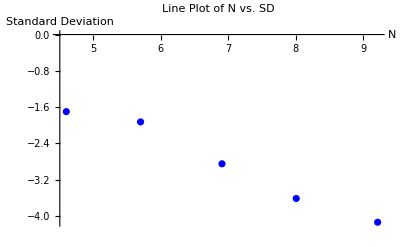

```mathematica
scatterplot=ListPlot[Transpose[{NVals,SDVals}],PlotStyle->Blue,AxesLabel->{"N","Standard Deviation"},PlotLabel->"Line Plot of N vs. SD"]
```

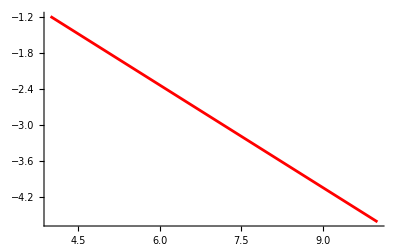

-0.570386

```mathematica
model=LinearModelFit[Transpose[{NVals,SDVals}],x,x];
modelplot= Plot[model[x],{x,4,10},PlotStyle->Red]
slope=model["BestFitParameters"][[2]];  

slope
```

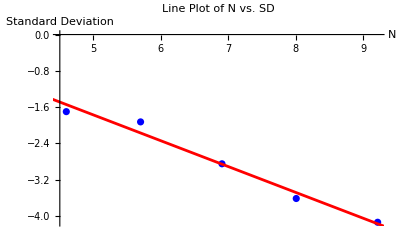

```mathematica
plot12=Show[scatterplot,modelplot]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.0847 | 0.358825 | 3.02293 | 0.0566275
x | -0.570386 | 0.050706 | -11.2489 | 0.00150634

```mathematica
data2 = {{100,0.048},{300,0.026},{1000,0.01},{3000,0.006},{10000,0.002}}
```

{{100,0.048},{300,0.026},{1000,0.01},{3000,0.006},{10000,0.002}}

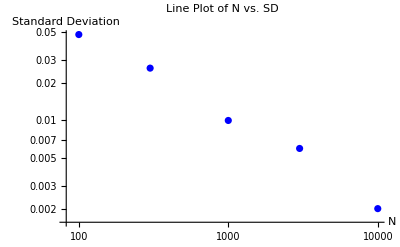

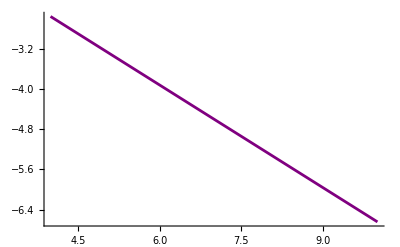

-0.680403

```mathematica
scatterplot=ListLogLogPlot[data2,PlotStyle->Blue,AxesLabel->{"N","Standard Deviation"},PlotLabel->"Line Plot of N vs. SD"]
model=LinearModelFit[Log[{{100,0.048},{300,0.026},{1000,0.01},{3000,0.006},{10000,0.002}}],x,x];
modelplot= Plot[model[x],{x,4,10},PlotStyle->Purple]
slope=model["BestFitParameters"][[2]];  
slope
```

-0.680403

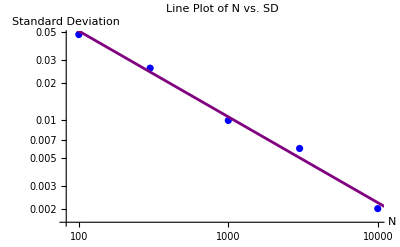

```mathematica
-0.6804032905926111

plot08=Show[scatterplot,modelplot]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.161324 | 0.26162 | 0.616637 | 0.58111
x | -0.680403 | 0.0369698 | -18.4043 | 0.000350038

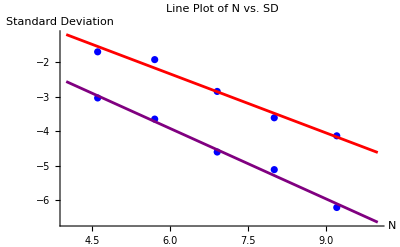

```mathematica
Show[plot12,plot08,PlotRange->All]
```